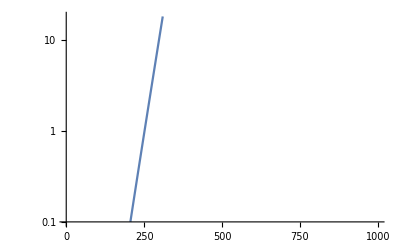

```mathematica
Clear["Global`*"]
dim=3;(*dimension*)
w =10^-6;
R=3 w;n=20;
m=6 * 1.66 10^-27;
L=w;
h=6.626 10^-34;
hb= h/(2Pi);
f={26.22,26.22,4.6} 10^3;
f=GeometricMean@f;
hl=√(hb/(m 2 Pi f));
leff=1/(√(4/w^2+1/hl^2));
V=104.52 1000 h;
Eg=-V+h f/2;
FGR[omega_]:=(hl hb^2)/(V^2 leff^2)√((Pi(hb omega+Eg))/(2m))Exp[m omega leff^2/hb]
LogPlot[2Pi FGR[x 1000 2 Pi],{x,100,400},PlotRange->{{0,1000},{0.1,17.9}}]
```